```mathematica
Quit[]
```

### α

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
C1=-7/24;
C2=-80507/27648 Zeta[3] - 2/3 Zeta[2](1/3 Log[2]+1)-58933/124416;
C3=1/9 (Zeta[2]+2479/3456);
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
(**)
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
(**)
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2-β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+C1(αsNf[Q,f]/π)^2+(C2+(f-1)C3) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,5],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,5],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,5],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,5],Q≥Mt}}]
αs[2]
```

0.293359

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118394

```mathematica
(*LQs[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2](*Does not depend on "f" here*)
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2-β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]](*Does not depend at all of the Mαs3Loop*)
```

0.214266

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]](*Does not depend at all of the Mαs3Loop as well*)
```

0.0903085

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]](*So the suposed problem come from either the definition of the β or the definition of the αsNf4Loop*)
```

0.305202

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]](*It normal that I don't get back the experimental result because we are calculate them only at 4-loop of perturbation, thus they numerical value is not exactly the same, they need to be calculate at an infinite loop precision to get back the experimental results.*)
```

0.380206

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213008

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0903602

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.296718

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.341903

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231277

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0937725

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.333952

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.387775

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0898814

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0437312

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.123351

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.148426

```mathematica
αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}
```

0.217831

```mathematica
αsNf3Loop[Mb,4]/.{Λ->Λ3LoopNf4}
```

0.217831

```mathematica
αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}
```

0.352411

```mathematica
αsNf3Loop[Mc,3]/.{Λ->Λ3LoopNf3}
```

0.352411

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
(**)
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
(**)
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2-β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ2Loop[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+C1(αsNf[Q,f]/π)^2+(C2+(f-1)C3) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+C1(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,5],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,5],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,5],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,5],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,5],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,5],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,5],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,5],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.288359

0.290285

0.310311

0.270646

```mathematica
αs[MZ]
αs3Loop[MZ]
αs2Loop[MZ]
αs1Loop[MZ]
```

0.118394

0.118394

0.118394

«1 more identical outputs»

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.05531

4.49166

12.1604

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.0649

20.322

52.2911

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1918.32

1848.52

3963.76

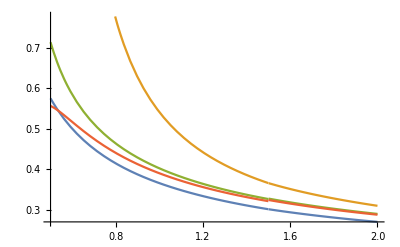

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

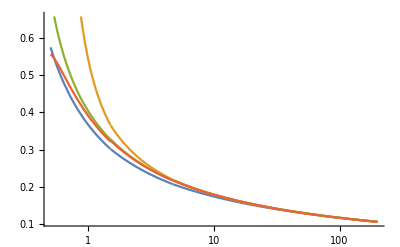

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### meson

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
t=FindRoot[αs1Loop[mu]==0.214850,{mu,1}][[1,2]]
mb=FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mb)
4*a
```

4.09968

4.7704

0.21485

0.8594

```mathematica
dE=-(4/3*a )^2/4
Mqq=PlusMinus[(2+dE)mb,0*mb]
```

-0.0205158

9.44293±0.

```mathematica
t=FindRoot[αs2Loop[mu]==0.227325,{mu,1}][[1,2]]
mb=FindRoot[t==fudge αs2Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mb)
4*a
```

4.42675

4.86831

0.227325

0.9093

```mathematica
Around[-9.15319438515637 10^-9,1.670345994080632 10^(-11)]/0.0001^2+ 16/18
```

-0.02640.0017

```mathematica
dE=-0.06031780502243687
Mqq=PlusMinus[(2+dE)mb,9.97823248953851*10^-5*mb]
```

-0.0603178

9.44297±0.000485771

```mathematica
t=FindRoot[αs3Loop[mu]==0.222492,{mu,1}][[1,2]]
mb=FindRoot[t==fudge αs3Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mb)
4*a
```

4.42291

4.96974

0.222492

0.889968

```mathematica
dE=-0.1000594894410938
Mqq=PlusMinus[(2+dE)mb,0.00010053052285862655*mb]
```

-0.100059

9.44222±0.000499611

```mathematica
t=FindRoot[αs1Loop[mu]==.282678,{mu,1}][[1,2]]
mc=FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mc)
4*a
```

1.76623

1.56206

0.282678

1.13071

```mathematica
dE=-0.14502484940651247
Mqq=PlusMinus[(2+dE)mc,0.00019066112136855817 mc]
```

-0.145025

2.89757±0.000297823

```mathematica
t=FindRoot[αs2Loop[mu]==0.313613,{mu,1}][[1,2]]
mc=FindRoot[t==fudge αs2Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mc)
4*a
```

2.07503

1.65413

0.313613

1.25445

```mathematica
dE=-0.14502484940651247
Mqq=PlusMinus[(2+dE)mc,0.00019066112136855817 mc]
```

-0.145025

3.06838±0.000315379

```mathematica
t=FindRoot[αs3Loop[mu]==0.297100,{mu,1}][[1,2]]
mc=FindRoot[t==fudge αs3Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mc)
4*a
```

2.10536

1.77159

0.2971

1.1884

```mathematica
dE=-0.2676441299683938
Mqq=PlusMinus[(2+dE)mc,0.0002475933366091873*mc]
```

-0.267644

3.06903±0.000438634

### baryon

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

Null

Null

«2 more identical outputs»

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

Null

Null

«3 more identical outputs»

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

Null

Null

«3 more identical outputs»

```mathematica
Null
```

Null

Null

```mathematica
Null
```

```mathematica
Null
```

Null

Null

Null

«3 more identical outputs»

```mathematica
Null
```

Null

Null

### tetra

```mathematica
Clear[mu];
```

```mathematica
m=FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}][[1,2]]
```

```mathematica
fudge=4;
```

```mathematica
t=FindRoot[mu==4 αs1Loop[mu]*mb,{mu,10000}][[1,2]]
t/mb
m=FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4m)
4*a
```

4.16505

0.855543

4.86831

0.213886

0.855543

```mathematica
dEE = -Around[-0.042299853565*m*1000,0.0011807932597*m*1000]
dE=-0.042299853565
Mqqq=Around[(4+dE)m,3.381184230*10^(-5)*m]
```

202.6.

-0.0422999

18.879810.00016

```mathematica
mredbbcc=4mb mc/(2mb + 2 mc)
mredbccc=4mb mc/(3mc + mb)
mredbbbc=4mb mc/(mc +3 mb)
```

2.35347

3.15194

1.87778

```mathematica
mbcccLO
```

3.15194

```mathematica
t=FindRoot[mu==4 αs2Loop[mu]*mredbbbc,{mu,10000}][[1,2]]
t/mredbbbc
m=FindRoot[t==fudge αs2Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mredbbbc)
4*a
mredbbbc
mb/mredbbbc
mc/mredbbbc
```

2.33965

1.18097

1.98113

0.295242

1.18097

1.98113

2.45734

0.834944

```mathematica
mcNNLO/ mbbbcNNLO
mbNNLO/ mbbbcNNLO
 mbbbcNNLO
```

0.839119

2.35393

2.11125

```mathematica
Around[-0.12490925789949929,0.000333398228]
```

```mathematica
dEE = -Around[-0.003810657167639694*mredbbbc*1000,0.0015454234491601216*mredbbbc*1000]
dE=-0.0120637533206713
MB=Around[mc+3mb+dE mredbbbcL,0.0006106170054059559*mredbbbc]
```

```mathematica
dE=-0.26802448832
MB=Around[3mcNNLO+mbNNLO+dE mbcccNNLO,0.0006742333757*mbcccNNLO]

dE=-0.381592079
MB=Around[2mcNNLO+2mbNNLO+dE mbcNNLO,0.0010400334*mbcNNLO]

dE=-0.415210596
MB=Around[2mcNNLO+2mbNNLO+dE mbcNNLO,0.0009414291*mbcNNLO]

dE=-0.619171884
MB=Around[3mbNNLO+mcNNLO+dE mbbbcNNLO,0.008956996*mbbbcNNLO]
```

-0.268024

9.36670.0023

-0.381592

12.48590.0027

-0.415211

12.39810.0025

-0.619172

15.3740.019

-0.124909

9.42140.0011

-0.215474

12.51280.0007

-0.245098

12.43970.0008

-0.371318

15.5230.005

```mathematica
mcNLO
```

1.65413

```mathematica
mb
```

4.7704

```mathematica
mcLO=1.56206;
mcNLO= 1.65413;
mcNNLO=1.77159;

mbLO=4.770399859803271;
mbNLO=4.86831;
mbNNLO=4.96974;

mbcLO=2 (4.770399859803271 1.56206)/(4.770399859803271+1.56206)
mbcNLO=2(4.86831 1.65413)/(4.86831+1.65413)
mbcNNLO=2(4.96974 1.77159)/(4.96974+ 1.77159)

mbbbcLO=4 (4.770399859803271 1.56206)/(3 4.770399859803271+1.56206);
mbbbcNLO=4(4.86831 1.65413)/(3 4.86831+1.65413);
mbbbcNNLO=4(4.96974 1.77159)/(3 4.96974+ 1.77159);

mbcccLO=4 (4.770399859803271 1.56206)/(4.770399859803271+3 1.56206);
mbcccNLO=4(4.86831 1.65413)/(4.86831+3 1.65413);
mbcccNNLO=4(4.96974 1.77159)/(4.96974+ 3 1.77159);
```

2.35348

2.46927

2.61205

```mathematica
mbLO/mbcLO
mbNLO/mbcNLO
mbNNLO/mbcNNLO

mcLO/mbcLO
mcNLO/mbcNLO
mcNNLO/mbcNNLO

mbLO/mbbbcLO
mbNLO/mbbbcNLO
mbNNLO/mbbbcNNLO

mcLO/mbbbcLO
mcNLO/mbbbcNLO
mcNNLO/mbbbcNNLO
```

2.02696

1.97156

1.90262

0.663724

0.669887

0.678238

2.54044

2.45734

2.35393

0.831862

0.834944

0.839119

```mathematica
mcNLO Around[-0.1016971729115,0.00037173717236]
```

-0.16820.0006

```mathematica
mbcNLO Around[-0.080380237408,0.0002643571452]
```

-0.19850.0007

```mathematica
Print["cccc"]

-(Around[-0.07330052,0.000056872]+(4/3 0.282678)^2/2)*mcLO 1000

-(Around[-0.3023130,0.00118079]-Around[-0.2883841,0.00041846])*mcNLO 1000

-(Around[-0.5597242668529847,0.002702299907073]-Around[-0.5335849636075951,0.00090084581222])*mcNNLO 1000

Print["bccc"]

-(Around[-0.0340911021911165,0.0000742333757]mbcccLO+(4/3 0.236339)^2/4(mbcLO+mcLO))*1000 

-(Around[-0.12490925789949929,0.000333398228]mbcccNLO-( mbcccNLO Around[-0.0665783189665,0.00012975]+mbcccNLO Around[-0.050112980,0.0002122404271]))*1000 

-(Around[-0.26802448832,0.00065536065]mbcccNNLO-(mbcccNNLO Around[-0.13856671266678,0.0005060118]+mbcccNNLO Around[-0.11302664338,0.0002572147]))*1000 

Print["bcbc"]

-(Around[-0.061043867110541127,0.00008516723528]+(4/3 0.253887)^2/2)*1000 mbcLO

-(Around[-0.21547434178107575,0.0002921919783]-2*Around[-0.10219824993605,0.00056611117])*1000 mbcNLO

-(Around[-0.3815920796996,0.001040033490]-2Around[-0.17925124343,0.00037717876])*1000 mbcNNLO

Print["bbcc"]

-(Around[-0.07986690601022971,0.00003575581529600]mbcLO+(4/3 0.253887)^2/4(mbLO+mcLO))*1000 

-(Around[-0.24509825049650058,0.00032244328]mbcNLO-(Around[-0.07755018109110,0.00017408783]+Around[-0.159571318241,0.0008739404])(mbcNLO))*1000 

-(Around[-0.41521059642188,0.0009414291410]mbcNNLO-(Around[-0.2448929281290,0.0003779248824]+Around[-0.1473846540419,0.000305025])(mbcNNLO))*1000 

Print["bbbc"]

-(Around[-0.12367954170310144,0.00021267741295]mbbbcLO+(4/3 0.26908)^2/2/2(mbcLO+mbLO))*1000 

-(Around[-0.3713179407985204,0.0023770407]mbbbcNLO-(mbbbcNLO Around[-0.218248391842137,0.001165855645]+mbbbcNLO Around[-0.141639640222,0.00033521000]))*1000 

-(Around[-0.61917188479,0.0089569963514]mbbbcNNLO- ( mbbbcNNLO Around[-0.24657681414,0.00134739602]+mbbbcNNLO Around[-0.33140075251,0.0004414036774]))*1000 

Print["bbbb"]

-(Around[-0.04229985356519324,0.000038118423559950522913]+(4/3 0.21485)^2/2)*1000*mbLO
 
-(Around[-0.12586424301766927,0.00019392288564]-Around[-0.1208296862644231,0.00013044332403071])*1000*mbNLO

-(Around[-0.21064525497988354,0.0002346802823177]-Around[-0.20060436070076992,0.000370481479510])*1000*mbNNLO
```

```mathematica
Around[-0.61917188479,0.0089569963514]
```

-0.6190.009

```mathematica
(4/3 0.21485)^2/2
```

0.0410316

```mathematica
0.4*500*0.1^2 *9/16
250*5*0.05^2*9/16
300*10*0.025^2*9/16
300*40*0.01^2*9/16
400*4800*0.001^2*9/16
400*400000*0.0001^2*9/16
```

1.125

1.75781

1.05469

0.675

1.08

0.9

```mathematica
3.06865+6.26505
```

9.3337

```mathematica
-(Around[6.1338,0.0001]-2*3.06865)*1000
-(Around[6.115,0.001]-Around[-0.11749691978509443,0.0003380718977498816])*1000
-(Around[6.085,0.001]-2*Around[3.0690,0.0004])*1000

-(Around[9.438,0.003]- 3.06865-6.26505)*1000
-(Around[9.398,0.003]-  Around[3.0684,0.0003]-Around[6.273,0.002])*1000
-(Around[9.359,0.002]- Around[3.0690,0.0004]-Around[6.279,0.003])*1000

-(Around[12.5207,0.0002]-2 6.26505)*1000
-(Around[12.5138,0.0009]-Around[-0.20240937974416873,0.0002063616634262434])*1000
-(Around[12.4862,0.0009]-Around[6.279,0.003])*1000

-(Around[12.483,0.003]- 3.06865-9.44295)*1000
-(Around[12.453,0.006]-  Around[9.4430,0.0005]-  Around[3.0684,0.0003])*1000
-(Around[12.405,0.007]- Around[3.0690,0.0004]- Around[9.4422,0.0005])*1000

-(Around[15.648,0.003]- 6.26505-9.44295)*1000
-(Around[15.568,0.004]- Around[6.273,0.002]-  Around[9.4430,0.0005])*1000
-(Around[15.431,0.008]- Around[9.4422,0.0005]- Around[6.279,0.003])*1000

-(Around[18.8798,0.0001]-2*9.44295)*1000
-(Around[18.860,0.001]-2*Around[9.4430,0.0005])*1000
-(Around[18.832,0.001]-2*Around[9.4422,0.0005])*1000
```

3.500.10

21.81.2

53.01.3

-104.33.0

-57.4.

-11.4.

9.400.20

32.4.

72.6.

28.63.0

58.6.

106.7.

60.03.0

148.5.

290.9.

6.100.10

26.01.4

52.41.4

```mathematica
((6+Around[-0.07761536869704458,0.00025052247292661344])1.56206-2 Around[4.62670,0.00002])*1000
```

-2.30.4

```mathematica
((6+Around[-0.3505877747185328,0.00127421697554791])1.65413-2 Around[4.6718,0.0007])*1000
```

1.32.5

```mathematica
((6+Around[-0.13600220935216176,])4.77041-2 Around[14.20641,0.00003])*1000
```

-5.01.4

```mathematica
((6+Around[-0.1450423549804203,0.0006670478736518825])4.86831-2 Around[14.2573,0.0007])*1000
```

-10.93.5

-1.02.2

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
t=FindRoot[αs1Loop[mu]==0.02,{mu,1}][[1,2]]
FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}]
```

1.34563×10^18

{mQ→10000.}

```mathematica
mbmb1=4.77041;
mcmc1=1.56206;
mbmb2=4.86886;
mcmc2=1.65234;
mbmb3=4.96983;
mcmc3=1.77092;
mbbcc1=  2 4.77041*1.56206/(4.77041+1.56206);
mbbcc2=2 4.86886*1.65234/(4.86886+1.65234);
mbbcc3=2*4.96983*1.77092/(4.96983+1.77092);
mbbbc1= 4 4.77041*1.56206/(3 4.77041+1.56206);
mbbbc2= 4 4.86886*1.65234/(3 4.86886+1.65234);
mbbbc3= 4 4.96983*1.77092/(3 4.96983+1.77092);
mcccb1= 4 4.77041*1.56206/( 4.77041+3 1.56206);
mcccb2= 4 4.86886*1.65234/( 4.86886+3 1.65234);
mcccb3= 4 4.96983*1.77092/( 4.96983+3 1.77092);
```

```mathematica
Subscript[mb, bcbc1]=9.44295/(2-2.86482706*10^-2);
Subscript[mc, bcbc1]=3.06865/(2-2.86482706*10^-2);
mrun1=  2 Subscript[mb, bcbc1]*Subscript[mc, bcbc1]/(Subscript[mb, bcbc1]+Subscript[mc, bcbc1]);
Subscript[mb, bcbc1]/mrun1
Subscript[mc, bcbc1]/mrun1
Subscript[mb, bbbc1]=9.44295/(2-3.21795762*10^-2);
Subscript[mc, bbbc1]=3.06865/(2-3.21795762*10^-2);
mrunb1=  4 Subscript[mb, bbbc1]*Subscript[mc, bbbc1]/(3 Subscript[mb, bbbc1]+Subscript[mc, bbbc1]);
Subscript[mb, bbbc1]/mrunb1
Subscript[mc, bbbc1]/mrunb1
Subscript[mb, cccb1]=9.44295/(2-2.48249435*10^-2);
Subscript[mc, cccb1]=3.06865/(2-2.48249435*10^-2);
mrunc1=  4 Subscript[mb, cccb1]*Subscript[mc, cccb1]/(Subscript[mb, cccb1]+3 Subscript[mc, cccb1]);
Subscript[mb, cccb1]/mrunc1
Subscript[mc, cccb1]/mrunc1

Subscript[mb, bcbc2]=9.44295/(2-0.10125203551696758);
Subscript[mc, bcbc2]=3.06865/(2-0.10125203551696758);
mrun2=  2 Subscript[mb, bcbc2]*Subscript[mc, bcbc2]/(Subscript[mb, bcbc2]+Subscript[mc, bcbc2]);
Subscript[mb, bcbc1]/mrun2
Subscript[mc, bcbc1]/mrun2
Subscript[mb, bbbc2]=9.44295/(2-0.12313396381500322);
Subscript[mc, bbbc2]=3.06865/(2-0.12313396381500322);
mrunb2=  4 Subscript[mb, bbbc2]*Subscript[mc, bbbc2]/(3 Subscript[mb, bbbc2]+Subscript[mc, bbbc2]);
Subscript[mb, bbbc2]/mrunb2
Subscript[mc, bbbc2]/mrunb2
Subscript[mb, cccb2]=9.44295/(2-0.08066989602983878);
Subscript[mc, cccb2]=3.06865/(2-0.08066989602983878);
mrunc2=  4 Subscript[mb, cccb2]*Subscript[mc, cccb2]/(Subscript[mb, cccb2]+3 Subscript[mc, cccb2]);
Subscript[mb, cccb2]/mrunc2
Subscript[mc, cccb2]/mrunc2

Subscript[mb, bcbc3]=9.44295/(2-0.17831483792710215);
Subscript[mc, bcbc3]=3.06865/(2-0.17831483792710215);
mrun3=  2 Subscript[mb, bcbc3]*Subscript[mc, bcbc3]/(Subscript[mb, bcbc3]+Subscript[mc, bcbc3]);
Subscript[mb, bcbc3]/mrun3
Subscript[mc, bcbc3]/mrun3
Subscript[mb, bbbc3]=9.44295/(2-0.22172372727825526);
Subscript[mc, bbbc3]=3.06865/(2-0.22172372727825526);
mrunb3=  4 Subscript[mb, bbbc3]*Subscript[mc, bbbc3]/(3 Subscript[mb, bbbc3]+Subscript[mc, bbbc3]);
Subscript[mb, bbbc3]/mrunb3
Subscript[mc, bbbc3]/mrunb3
Subscript[mb, cccb3]=9.44295/(2-0.13841175779511156);
Subscript[mc, cccb3]=3.06865/(2-0.13841175779511156);
mrunc3=  4 Subscript[mb, cccb3]*Subscript[mc, cccb3]/(Subscript[mb, cccb3]+3 Subscript[mc, cccb3]);
Subscript[mb, cccb3]/mrunc3
Subscript[mc, cccb3]/mrunc3
```

```mathematica
Max[1,mu/.FindRoot[mu==fudge αs2Loop[mu]mcccb2,{mu,10}]]//αs2Loop
%*4*mcccb2/mrunc2
```

0.253247

1.02449

```mathematica
PlusMinus[0.002809200164831196mrun1,0.0004949302174303964mrun1]
```

0.00660071±0.00116293

```mathematica
PlusMinus[-0.006844279250047077mrun2,0.0009900615853415567mrun2]
```

-0.0166968±0.00241528

```mathematica
-0.027884665103933726mrun3
```

-0.0709029

```mathematica
PlusMinus[2 Subscript[mb, bcbc3]+2 Subscript[mc, bcbc3]-0.4506540799065757mrun3,0.0035229718881632515mrun3]
```

12.5904±0.00895794

```mathematica
PlusMinus[Subscript[mb, bcbc3]+Subscript[mc, bcbc3]-0.3620389329220557 mrun3/2,0.00035714962908257744mrun3/2]
```

6.40786±0.000454066

```mathematica
PlusMinus[3 Subscript[mc, cccb3]+Subscript[mb, cccb3]-0.28843620942924264 mrunc3,0.0024163845225604027mrunc3]
```

9.05473±0.0080676

```mathematica
PlusMinus[3 Subscript[mb, bbbc3]+Subscript[mc, bbbc3]-0.6204680633555779mrunb3,0.011143729406346406mrunb3]
```

15.9943±0.028893

### meson wild

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.91028,4.67845,4.30524,3.92292,3.5298,3.12353,2.70063,2.25564}

```mathematica
t=FindRoot[αs1Loop[mu]==0.21485,{mu,1}][[1,2]]
mb=FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mb)
4*a
```

4.12318

4.79774

0.21485

0.8594

```mathematica
dE=-(4/3*a )^2/4
Mqq=PlusMinus[(2+dE)mb,0*mb]
```

-0.00444444

1714.19±0.

```mathematica
t=FindRoot[αs2Loop[mu]==0.224010,{mu,1}][[1,2]]
mb=FindRoot[t==fudge αs2Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mb)
4*a
```

4.38036

4.88857

0.22401

0.89604

```mathematica
Around[-9.15319438515637 10^-9,1.670345994080632 10^(-11)]/0.0001^2+ 16/18
```

-0.02640.0017

```mathematica
dE=-0.06031780502243687
Mqq=PlusMinus[(2+dE)mb,9.97823248953851*10^-5*mb]
```

-0.0603178

9.44297±0.000485771

```mathematica
t=FindRoot[αs3Loop[mu]==0.221400,{mu,1}][[1,2]]
mb=FindRoot[t==fudge αs3Loop[t]mQ,{mQ,10000}][[1,2]](*It change again*)
a=t/(4mb)
4*a
```

4.42475

4.99633

0.2214

0.8856

```mathematica
mb=FindRoot[t==fudge αs3Loop[t]mQ,{mQ,10000}][[1,2]](*It change again*)
```

4.8611

```mathematica
NumberForm[mb,16]
```

4.861098186031471

```mathematica
dE=-0.1000594894410938
Mqq=PlusMinus[(2+dE)mb,0.00010053052285862655*mb]
```

-0.100059

9.44222±0.000499611

```mathematica
t=FindRoot[αs1Loop[mu]==.3,{mu,1}][[1,2]]
mc=FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mc)
4*a
```

1.51413

1.26177

0.3

1.2

```mathematica
dE=-0.14502484940651247
Mqq=PlusMinus[(2+dE)mc,0.00019066112136855817 mc]
```

-0.145025

2.89757±0.000297823

```mathematica
t=FindRoot[αs2Loop[mu]==0.313613,{mu,1}][[1,2]]
mc=FindRoot[t==fudge αs2Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mc)
4*a
```

1.94933

1.55393

0.313613

1.25445

```mathematica
dE=-0.14502484940651247
Mqq=PlusMinus[(2+dE)mc,0.00019066112136855817 mc]
```

-0.145025

3.06838±0.000315379

```mathematica
t=FindRoot[αs3Loop[mu]==0.287300,{mu,1}][[1,2]]
mc=FindRoot[t==fudge αs3Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mc)
4*a
```

2.0409

1.77593

0.2873

1.1492

```mathematica
dE=-0.2676441299683938
Mqq=PlusMinus[(2+dE)mc,0.0002475933366091873*mc]
```

-0.267644

3.06903±0.000438634

### tetra wild

```mathematica
Clear[mu];
```

```mathematica
m=FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}][[1,2]]
```

1.26177

```mathematica
fudge=4;
```

```mathematica
t=FindRoot[mu==4 αs1Loop[mu]*mb,{mu,10000}][[1,2]]
t/mb
m=FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4m)
4*a
```

343.601

0.4

859.002

0.1

0.4

```mathematica
mc
```

1.26177

```mathematica
dEE = -Around[-0.042299853565*m*1000,0.0011807932597*m*1000]
dE=-0.042299853565
Mqqq=Around[(4+dE)m,3.381184230*10^(-5)*m]
```

3.630.1010^4

-0.0422999

3399.6730.029

```mathematica
mredbbcc=4mb mc/(2mb + 2 mc)
mredbccc=4mb mc/(3mc + mb)
mredbbbc=4mb mc/(mc +3 mb)
```

2.51985

5.02496

1.68154

```mathematica
mbcccLO
```

3.15194

```mathematica
t=FindRoot[mu==4 αs2Loop[mu]*mredbbbc,{mu,10000}][[1,2]]
t/mredbbbc
m=FindRoot[t==fudge αs2Loop[t]mQ,{mQ,10000}][[1,2]]
a=t/(4mredbbbc)
4*a
mredbbbc
mb/mredbbbc
mc/mredbbbc
```

2.33965

1.18097

1.98113

0.295242

1.18097

1.98113

2.45734

0.834944

```mathematica
mcNNLO/ mbbbcNNLO
mbNNLO/ mbbbcNNLO
 mbbbcNNLO
```

0.839119

2.35393

2.11125

```mathematica
Around[-0.12490925789949929,0.000333398228]
```

```mathematica
dEE = -Around[-0.003810657167639694*mredbbbc*1000,0.0015454234491601216*mredbbbc*1000]
dE=-0.0120637533206713
MB=Around[mc+3mb+dE mredbbbcL,0.0006106170054059559*mredbbbc]
```

```mathematica
dE=-0.26802448832
MB=Around[3mcNNLO+mbNNLO+dE mbcccNNLO,0.0006742333757*mbcccNNLO]

dE=-0.381592079
MB=Around[2mcNNLO+2mbNNLO+dE mbcNNLO,0.0010400334*mbcNNLO]

dE=-0.415210596
MB=Around[2mcNNLO+2mbNNLO+dE mbcNNLO,0.0009414291*mbcNNLO]

dE=-0.619171884
MB=Around[3mbNNLO+mcNNLO+dE mbbbcNNLO,0.008956996*mbbbcNNLO]
```

-0.268024

9.36670.0023

-0.381592

12.48590.0027

-0.415211

12.39810.0025

-0.619172

15.3740.019

-0.124909

9.42140.0011

-0.215474

12.51280.0007

-0.245098

12.43970.0008

-0.371318

15.5230.005

```mathematica
mcNLO
```

1.65413

```mathematica
mb
```

4.7704

```mathematica
mcLO=1.56206;
mcNLO= 1.65413;
mcNNLO=1.77159;

mbLO=4.770399859803271;
mbNLO=4.86831;
mbNNLO=4.96974;

mbcLO=2 (4.770399859803271 1.56206)/(4.770399859803271+1.56206)
mbcNLO=2(4.86831 1.65413)/(4.86831+1.65413)
mbcNNLO=2(4.96974 1.77159)/(4.96974+ 1.77159)

mbbbcLO=4 (4.770399859803271 1.56206)/(3 4.770399859803271+1.56206);
mbbbcNLO=4(4.86831 1.65413)/(3 4.86831+1.65413);
mbbbcNNLO=4(4.96974 1.77159)/(3 4.96974+ 1.77159);

mbcccLO=4 (4.770399859803271 1.56206)/(4.770399859803271+3 1.56206);
mbcccNLO=4(4.86831 1.65413)/(4.86831+3 1.65413);
mbcccNNLO=4(4.96974 1.77159)/(4.96974+ 3 1.77159);
```

2.35348

2.46927

2.61205

```mathematica
mbLO/mbcLO
mbNLO/mbcNLO
mbNNLO/mbcNNLO

mcLO/mbcLO
mcNLO/mbcNLO
mcNNLO/mbcNNLO

mbLO/mbbbcLO
mbNLO/mbbbcNLO
mbNNLO/mbbbcNNLO

mcLO/mbbbcLO
mcNLO/mbbbcNLO
mcNNLO/mbbbcNNLO
```

2.02696

1.97156

1.90262

0.663724

0.669887

0.678238

2.54044

2.45734

2.35393

0.831862

0.834944

0.839119

```mathematica
mcNLO Around[-0.1016971729115,0.00037173717236]
```

-0.16820.0006

```mathematica
mbcNLO Around[-0.080380237408,0.0002643571452]
```

-0.19850.0007

```mathematica
Print["cccc"]

-(Around[-0.07330052,0.000056872]+(4/3 0.282678)^2/2)*mcLO 1000

-(Around[-0.3023130,0.00118079]-Around[-0.2883841,0.00041846])*mcNLO 1000

-(Around[-0.5597242668529847,0.002702299907073]-Around[-0.5335849636075951,0.00090084581222])*mcNNLO 1000

Print["bccc"]

-(Around[-0.0340911021911165,0.0000742333757]mbcccLO+(4/3 0.236339)^2/4(mbcLO+mcLO))*1000 

-(Around[-0.12490925789949929,0.000333398228]mbcccNLO-( mbcccNLO Around[-0.0665783189665,0.00012975]+mbcccNLO Around[-0.050112980,0.0002122404271]))*1000 

-(Around[-0.26802448832,0.00065536065]mbcccNNLO-(mbcccNNLO Around[-0.13856671266678,0.0005060118]+mbcccNNLO Around[-0.11302664338,0.0002572147]))*1000 

Print["bcbc"]

-(Around[-0.061043867110541127,0.00008516723528]+(4/3 0.253887)^2/2)*1000 mbcLO

-(Around[-0.21547434178107575,0.0002921919783]-2*Around[-0.10219824993605,0.00056611117])*1000 mbcNLO

-(Around[-0.3815920796996,0.001040033490]-2Around[-0.17925124343,0.00037717876])*1000 mbcNNLO

Print["bbcc"]

-(Around[-0.07986690601022971,0.00003575581529600]mbcLO+(4/3 0.253887)^2/4(mbLO+mcLO))*1000 

-(Around[-0.24509825049650058,0.00032244328]mbcNLO-(Around[-0.07755018109110,0.00017408783]+Around[-0.159571318241,0.0008739404])(mbcNLO))*1000 

-(Around[-0.41521059642188,0.0009414291410]mbcNNLO-(Around[-0.2448929281290,0.0003779248824]+Around[-0.1473846540419,0.000305025])(mbcNNLO))*1000 

Print["bbbc"]

-(Around[-0.12367954170310144,0.00021267741295]mbbbcLO+(4/3 0.26908)^2/2/2(mbcLO+mbLO))*1000 

-(Around[-0.3713179407985204,0.0023770407]mbbbcNLO-(mbbbcNLO Around[-0.218248391842137,0.001165855645]+mbbbcNLO Around[-0.141639640222,0.00033521000]))*1000 

-(Around[-0.61917188479,0.0089569963514]mbbbcNNLO- ( mbbbcNNLO Around[-0.24657681414,0.00134739602]+mbbbcNNLO Around[-0.33140075251,0.0004414036774]))*1000 

Print["bbbb"]

-(Around[-0.04229985356519324,0.000038118423559950522913]+(4/3 0.21485)^2/2)*1000*mbLO
 
-(Around[-0.12586424301766927,0.00019392288564]-Around[-0.1208296862644231,0.00013044332403071])*1000*mbNLO

-(Around[-0.21064525497988354,0.0002346802823177]-Around[-0.20060436070076992,0.000370481479510])*1000*mbNNLO
```

```mathematica
Around[-0.61917188479,0.0089569963514]
```

-0.6190.009

```mathematica
(4/3 0.21485)^2/2
```

0.0410316

```mathematica
0.4*500*0.1^2 *9/16
250*5*0.05^2*9/16
300*10*0.025^2*9/16
300*40*0.01^2*9/16
400*4800*0.001^2*9/16
400*400000*0.0001^2*9/16
```

1.125

1.75781

1.05469

0.675

1.08

0.9

```mathematica
3.06865+6.26505
```

9.3337

```mathematica
-(Around[6.1338,0.0001]-2*3.06865)*1000
-(Around[6.115,0.001]-Around[-0.11749691978509443,0.0003380718977498816])*1000
-(Around[6.085,0.001]-2*Around[3.0690,0.0004])*1000

-(Around[9.438,0.003]- 3.06865-6.26505)*1000
-(Around[9.398,0.003]-  Around[3.0684,0.0003]-Around[6.273,0.002])*1000
-(Around[9.359,0.002]- Around[3.0690,0.0004]-Around[6.279,0.003])*1000

-(Around[12.5207,0.0002]-2 6.26505)*1000
-(Around[12.5138,0.0009]-Around[-0.20240937974416873,0.0002063616634262434])*1000
-(Around[12.4862,0.0009]-Around[6.279,0.003])*1000

-(Around[12.483,0.003]- 3.06865-9.44295)*1000
-(Around[12.453,0.006]-  Around[9.4430,0.0005]-  Around[3.0684,0.0003])*1000
-(Around[12.405,0.007]- Around[3.0690,0.0004]- Around[9.4422,0.0005])*1000

-(Around[15.648,0.003]- 6.26505-9.44295)*1000
-(Around[15.568,0.004]- Around[6.273,0.002]-  Around[9.4430,0.0005])*1000
-(Around[15.431,0.008]- Around[9.4422,0.0005]- Around[6.279,0.003])*1000

-(Around[18.8798,0.0001]-2*9.44295)*1000
-(Around[18.860,0.001]-2*Around[9.4430,0.0005])*1000
-(Around[18.832,0.001]-2*Around[9.4422,0.0005])*1000
```

3.500.10

21.81.2

53.01.3

-104.33.0

-57.4.

-11.4.

9.400.20

32.4.

72.6.

28.63.0

58.6.

106.7.

60.03.0

148.5.

290.9.

6.100.10

26.01.4

52.41.4

```mathematica
((6+Around[-0.07761536869704458,0.00025052247292661344])1.56206-2 Around[4.62670,0.00002])*1000
```

-2.30.4

```mathematica
((6+Around[-0.3505877747185328,0.00127421697554791])1.65413-2 Around[4.6718,0.0007])*1000
```

1.32.5

```mathematica
((6+Around[-0.13600220935216176,])4.77041-2 Around[14.20641,0.00003])*1000
```

-5.01.4

```mathematica
((6+Around[-0.1450423549804203,0.0006670478736518825])4.86831-2 Around[14.2573,0.0007])*1000
```

-10.93.5

-1.02.2

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
t=FindRoot[αs1Loop[mu]==0.02,{mu,1}][[1,2]]
FindRoot[t==fudge αs1Loop[t]mQ,{mQ,10000}]
```

1.34563×10^18

{mQ→10000.}

```mathematica
mbmb1=4.77041;
mcmc1=1.56206;
mbmb2=4.86886;
mcmc2=1.65234;
mbmb3=4.96983;
mcmc3=1.77092;
mbbcc1=  2 4.77041*1.56206/(4.77041+1.56206);
mbbcc2=2 4.86886*1.65234/(4.86886+1.65234);
mbbcc3=2*4.96983*1.77092/(4.96983+1.77092);
mbbbc1= 4 4.77041*1.56206/(3 4.77041+1.56206);
mbbbc2= 4 4.86886*1.65234/(3 4.86886+1.65234);
mbbbc3= 4 4.96983*1.77092/(3 4.96983+1.77092);
mcccb1= 4 4.77041*1.56206/( 4.77041+3 1.56206);
mcccb2= 4 4.86886*1.65234/( 4.86886+3 1.65234);
mcccb3= 4 4.96983*1.77092/( 4.96983+3 1.77092);
```

```mathematica
Subscript[mb, bcbc1]=9.44295/(2-2.86482706*10^-2);
Subscript[mc, bcbc1]=3.06865/(2-2.86482706*10^-2);
mrun1=  2 Subscript[mb, bcbc1]*Subscript[mc, bcbc1]/(Subscript[mb, bcbc1]+Subscript[mc, bcbc1]);
Subscript[mb, bcbc1]/mrun1
Subscript[mc, bcbc1]/mrun1
Subscript[mb, bbbc1]=9.44295/(2-3.21795762*10^-2);
Subscript[mc, bbbc1]=3.06865/(2-3.21795762*10^-2);
mrunb1=  4 Subscript[mb, bbbc1]*Subscript[mc, bbbc1]/(3 Subscript[mb, bbbc1]+Subscript[mc, bbbc1]);
Subscript[mb, bbbc1]/mrunb1
Subscript[mc, bbbc1]/mrunb1
Subscript[mb, cccb1]=9.44295/(2-2.48249435*10^-2);
Subscript[mc, cccb1]=3.06865/(2-2.48249435*10^-2);
mrunc1=  4 Subscript[mb, cccb1]*Subscript[mc, cccb1]/(Subscript[mb, cccb1]+3 Subscript[mc, cccb1]);
Subscript[mb, cccb1]/mrunc1
Subscript[mc, cccb1]/mrunc1

Subscript[mb, bcbc2]=9.44295/(2-0.10125203551696758);
Subscript[mc, bcbc2]=3.06865/(2-0.10125203551696758);
mrun2=  2 Subscript[mb, bcbc2]*Subscript[mc, bcbc2]/(Subscript[mb, bcbc2]+Subscript[mc, bcbc2]);
Subscript[mb, bcbc1]/mrun2
Subscript[mc, bcbc1]/mrun2
Subscript[mb, bbbc2]=9.44295/(2-0.12313396381500322);
Subscript[mc, bbbc2]=3.06865/(2-0.12313396381500322);
mrunb2=  4 Subscript[mb, bbbc2]*Subscript[mc, bbbc2]/(3 Subscript[mb, bbbc2]+Subscript[mc, bbbc2]);
Subscript[mb, bbbc2]/mrunb2
Subscript[mc, bbbc2]/mrunb2
Subscript[mb, cccb2]=9.44295/(2-0.08066989602983878);
Subscript[mc, cccb2]=3.06865/(2-0.08066989602983878);
mrunc2=  4 Subscript[mb, cccb2]*Subscript[mc, cccb2]/(Subscript[mb, cccb2]+3 Subscript[mc, cccb2]);
Subscript[mb, cccb2]/mrunc2
Subscript[mc, cccb2]/mrunc2

Subscript[mb, bcbc3]=9.44295/(2-0.17831483792710215);
Subscript[mc, bcbc3]=3.06865/(2-0.17831483792710215);
mrun3=  2 Subscript[mb, bcbc3]*Subscript[mc, bcbc3]/(Subscript[mb, bcbc3]+Subscript[mc, bcbc3]);
Subscript[mb, bcbc3]/mrun3
Subscript[mc, bcbc3]/mrun3
Subscript[mb, bbbc3]=9.44295/(2-0.22172372727825526);
Subscript[mc, bbbc3]=3.06865/(2-0.22172372727825526);
mrunb3=  4 Subscript[mb, bbbc3]*Subscript[mc, bbbc3]/(3 Subscript[mb, bbbc3]+Subscript[mc, bbbc3]);
Subscript[mb, bbbc3]/mrunb3
Subscript[mc, bbbc3]/mrunb3
Subscript[mb, cccb3]=9.44295/(2-0.13841175779511156);
Subscript[mc, cccb3]=3.06865/(2-0.13841175779511156);
mrunc3=  4 Subscript[mb, cccb3]*Subscript[mc, cccb3]/(Subscript[mb, cccb3]+3 Subscript[mc, cccb3]);
Subscript[mb, cccb3]/mrunc3
Subscript[mc, cccb3]/mrunc3
```

```mathematica
Max[1,mu/.FindRoot[mu==fudge αs2Loop[mu]mcccb2,{mu,10}]]//αs2Loop
%*4*mcccb2/mrunc2
```

0.253247

1.02449

```mathematica
PlusMinus[0.002809200164831196mrun1,0.0004949302174303964mrun1]
```

0.00660071±0.00116293

```mathematica
PlusMinus[-0.006844279250047077mrun2,0.0009900615853415567mrun2]
```

-0.0166968±0.00241528

```mathematica
-0.027884665103933726mrun3
```

-0.0709029

```mathematica
PlusMinus[2 Subscript[mb, bcbc3]+2 Subscript[mc, bcbc3]-0.4506540799065757mrun3,0.0035229718881632515mrun3]
```

12.5904±0.00895794

```mathematica
PlusMinus[Subscript[mb, bcbc3]+Subscript[mc, bcbc3]-0.3620389329220557 mrun3/2,0.00035714962908257744mrun3/2]
```

6.40786±0.000454066

```mathematica
PlusMinus[3 Subscript[mc, cccb3]+Subscript[mb, cccb3]-0.28843620942924264 mrunc3,0.0024163845225604027mrunc3]
```

9.05473±0.0080676

```mathematica
PlusMinus[3 Subscript[mb, bbbc3]+Subscript[mc, bbbc3]-0.6204680633555779mrunb3,0.011143729406346406mrunb3]
```

15.9943±0.028893